# All contributung processes

```mathematica
Clear[pl2]
```

## Definitions

```mathematica
Clear[ibar]
```

```mathematica
(*constraints and constants*)
GF = 1.16*^-5; (*everything in respective units of GeV*)
aEM = 1/137;
lambda = 0.22;
mu = 0.105;
Ncm = 1;
Ncq = 3;

C9low1f = -0.71;
C9high1f = -0.35;
C9low2f = -0.91;
C9high2f = -0.18;
bsmix = 2.5*^-11;
annRate = 7.5*^-10; (*1607.02457: 4*^-9; 1512.01991: 7.5*^-10, 1601.06590: 2.1*^-8 (most convincing)*)
abest = 2.87*^-9;
alow = 2.07*^-9;
ahigh = 3.67*^-9;

(*model parameters*)
mldiff = 200; (*16.08: 200 appears to be good: minimal because of slepton exclusions and maximal due to annihilation*)
mqdiff = 800;
gq2f = 0.04; (*good, comes from FN-charges*)
gq3f = 1;
gl2f = 2;
```

## Functions (g-2,Ann,Bs->mumu,Bs-Mix)

```mathematica
(*only for g-2; gl,m,Ml*)
tda[m_,M_]:=m^2/M^2 (*In Lavoura: t:=m^2/M^2 (t<1) but elsewhere t=M^2/m^2 because we have two Ms!*)
d[t_]:= (-2t^2+7t-11)/(18(t-1)^3)+(Log[t])/(3(t-1)^4)
dbar[t_]:=d[t]/t
c[t_]:= (t-3)/(4(t-1)^2)+(Log[t])/(2(t-1)^3) 
cbar[t_]:=-c[t]/t
i[t_]:=1/(12(t-1)^4)*(2+3t-6t^2+t^3+6t Log[t])
ibar[t_]:=i[1/t]/t
pda[g_,m_]:= g^2*mu^2/(6*Pi^2) * 1/(m+mldiff)^2
da[g_,m_,Qf_,Qb_]:=pda[g,m]*(Qf*(c[tda[m,m+mldiff]]+3/2*d[tda[m,m+mldiff]])+ Qb*(-cbar[tda[m,m+mldiff]]+3/2*dbar[tda[m,m+mldiff]]))
(*pda[g,m]*(Qf*i[tda[m,m+mldiff]] + Qb*ibar[tda[m,m+mldiff]])*)
```

```mathematica
FullSimplify[3/2d[x]+c[x]]
```

(2+x (3+(-6+x) x)+6 x Log[x])/(12 (-1+x)^4)

```mathematica
(*Annihilation into muons and quark pairs; gl,gq2,gq3,m,Ml,Mq*)
annDir[g_,m_,Nc_,mdiff_]:=Nc * g^4/(32*Pi)* m^2/((m+mdiff)^2+m^2)^2;
annMaj[g_,m_,Nc_,mdiff_]:=Nc * g^4/(48Pi) *m^2* ((m+mdiff)^4+m^4)/((m+mdiff)^2+m^2)^4 * 0.3^2(*1*^-5 today, 0.3 freezeout*)
annTot[ann_,gl2_,gq2_,gq3_,m_,Nq_,Nl_,ml_,mq_]:=ann[gl2,m,Nl,ml]+ann[gq2,m,Nq,mq]+2*ann[Sqrt[gq2*gq3],m,Nq,mq]+ann[gq3,m,Nq,mq] 
(*TODO: -coannihilations? - annihilation depends on group theory?*)
annTot[annMaj,0.9,1,0.2,200,3,1,200,800]
annTot[annDir,0.9,1,0.2,200,3,1,200,800]
da[1,200,0,+1]
```

3.32597×10^-10

7.72001×10^-9

3.81468×10^-10

```mathematica
(*Bs->mumu*)
xHad[m_,M_]:=M^2/m^2 (*Here t>1*)
Kshort[x_]:= (1-x+x^2Log[x])/(x-1)^2;
Kder[x_]:=(-1+x^2-2*x*Log[x])/(x-1)^3
Klong[x_,y_]:= (Kshort[x]-Kshort[y])/(x-y)
weak=4*GF/Sqrt[2]*(-1)*lambda^2*aEM/(4Pi);

fa23[pMod_,C_,m_,gm_]:=C*weak/pMod * m^2 /gm^2 * 1/Klong[xHad[m,m+mqdiff],xHad[m,m+mldiff]];
fa23BsMix[pMod_,m_]:=bsmix*m^2/(pMod *Kder[xHad[m,m+mqdiff]]);
```

## modA

```mathematica
preA=1/(128Pi^ 2); (*prefactor for hadronic processes (prefactor of tau-matrices = 0)*)
Qf1 = 0; (*electric charges for g-2*)
Qb1 = 1;
```

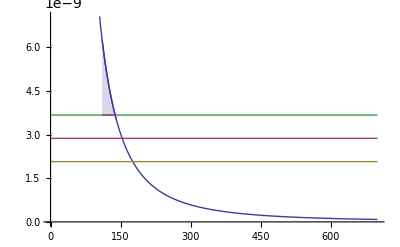

```mathematica
pldaA1 =Plot[{da[gl2f,m,Qf1,Qb1],abest,alow,ahigh},{m,0,700}];
pldaA2 =Plot[{da[gl2f,m,Qf1,Qb1],ahigh},{m,110.408,140.56},Filling->{1->{2}}];
Show[pldaA1,pldaA2]
```

```mathematica
FindRoot[da[gl2f,m,0,1]==ahigh,{m,100}]
FindRoot[da[gl2f,m,0,1]==alow,{m,150}]
```

{m→138.326}

{m→175.945}

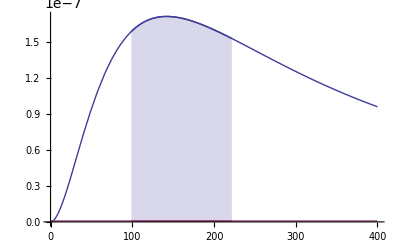

```mathematica
plannB1 = Plot[{annTot[annDir,gl2f,gq2f,gq3f,m,Ncq,Ncm,mldiff,mqdiff],annRate},{m,0,400}] ;
plannB2 = Plot[{annTot[annDir,gl2f,gq2f,gq3f,m,Ncq,Ncm,mldiff,mqdiff],annRate},{m,98.8348,221.841},Filling-> {1->{2}}] ;
Show[plannB1,plannB2]
```

```mathematica
FindRoot[annTot[annDir,gl2f,gq2f,gq3f,m,Ncq,Ncm,mldiff,mqdiff]==annRate,{m,100}]
FindRoot[annTot[annDir,gl2f,gq2f,gq3f,m,Ncq,Ncm,mldiff,mqdiff]==annRate,{m,400}]
```

{m→2.82341}

{m→7644.93}

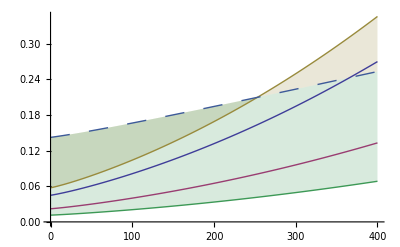

```mathematica
plBs1 = Plot[{fa23[preA,C9low1f,m,gl2f],fa23[preA,C9high1f,m,gl2f],fa23[preA,C9low2f,m,gl2f],fa23[preA,C9high2f,m,gl2f],Sqrt[fa23BsMix[preA,m]]},{m,0,400},PlotStyle->{Automatic,Automatic,Automatic,Automatic,Dashing[Large]},Filling->{5->{4},5->{3}}]
```

```mathematica
FindRoot[Sqrt[fa23BsMix[preA,m]]==fa23[preA,C9high1f,m,gl2f],{m,100}]
FindRoot[Sqrt[fa23BsMix[preA,m]]==fa23[preA,C9high2f,m,gl2f],{m,300}]
```

{m→-1054.41}

{m→-2038.03}

## modB

```mathematica
preB=5/(384Pi^ 2); (*prefactor for hadronic processes (prefactor of tau-matrices = 2/3)*)
Qf1 = 0; (*electric charges for g-2*)
Qb1 = 1;
Qf2 = 1; 
Qb2 = 0; (*only sum of respective charges seems to be important*)
gl2f = 2.3;
```

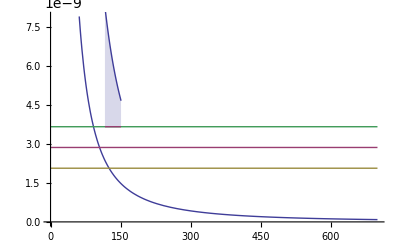

```mathematica
pldaB1 =Plot[{da[1,m,Qf1,Qb1] + da[gl2f,m,Qf2,Qb2],abest,alow,ahigh},{m,0,700}];
pldaB2 =Plot[{da[gl2f,m,Qf1,Qb1]+ da[gl2f,m,Qf2,Qb2],ahigh},{m,116.502,150.954},Filling->{1->{2}}];
Show[pldaB1,pldaB2]
(*effects: Ml higher -> lowers blue line (allowed region rise)   *)
```

```mathematica
FindRoot[da[gl2f,m,1,0]+da[gl2f,m,0,1]==ahigh,{m,100}]
FindRoot[da[gl2f,m,1,0]+da[gl2f,m,0,1]==alow,{m,100}]
```

{m→168.477}

{m→219.043}

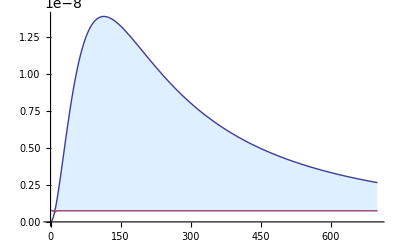

```mathematica
Plot[{annTot[annMaj,gl2f,gq2f,gq3f,m,Ncq,Ncm,mldiff,mqdiff],annRate},{m,0,700},Filling-> {1->{{2},{None,LightBlue}}}] 
(*effects: Ml higher -> lowers strongly blue line (allowed region shrinks)*)
(*         Mq higher -> almowst no effect for small gqs          *)
```

```mathematica
FindRoot[annTot[annMaj,gl2f,gq2f,gq3f,m,Ncq,Ncm,mldiff,mqdiff]==annRate,{m,100}]
FindRoot[annTot[annMaj,gl2f,gq2f,gq3f,m,Ncq,Ncm,mldiff,mqdiff]==annRate,{m,400}]
```

{m→9.31926}

{m→1515.55}

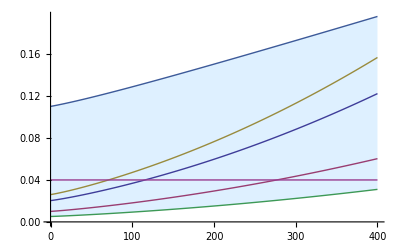

```mathematica
Plot[{fa23[preB,C9low1f,m,gl2f],fa23[preB,C9high1f,m,gl2f],fa23[preB,C9low2f,m,gl2f],fa23[preB,C9high2f,m,gl2f],Sqrt[fa23BsMix[preB,m]],gq2f},{m,0,400},Filling-> {5->{{4},{None,LightBlue}}}]
```

```mathematica
FindRoot[Sqrt[fa23BsMix[preB,m]]==fa23[preB,C9high1f,m,gl2f],{m,300}]
FindRoot[Sqrt[fa23BsMix[preB,m]]==fa23[preB,C9high2f,m,gl2f],{m,600}]
```

{m→-1795.87}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{m→-692.562}

```mathematica
xHad[m_,M_]:=M^2/m^2;
F1[x_]:= 1/(12(x-1)^4)*(x^3-6x^2+3x+2+6x Log[x]);
a[m_]:=gl2f^ 2/(6Pi^ 2) mu^ 2/m^2*(5*F1[xHad[m,m+mldiff]]+3/xHad[m,m+mldiff]*F1[1/xHad[m,m+mldiff]]);
5*F1[x];
FullSimplify[16/6*(-cbar[x]+3/2dbar[x])];
```

```mathematica
Plot[{2/x*F1[1/x]+5F1[x],5(c[x]+3/2d[x]) + -3(-cbar[x]+3/2dbar[x])},{x,2,100}];
Plot[{a[m],0.1da[gl2f,m,+5,-3]},{m,0,1000}];
Plot[a[m],{m,0,1000}];
xdir[x_,c_]:=x^2/((x+c)^2+x^2)^2;
xmaj[x_,c_]:=x^2*((x+c)^4+x^4)/((x+c)^2+x^2)^4;
light = 3*^10;
hbar = 4.1356*^-24/(2Pi);
sigma = 3*^-26;
omega = 0.12;
pre = 1/(light^3*hbar^2);
```

```mathematica
pre*sigma/omega
```

2.13727×10^-8

```mathematica
Plot[{xdir[x,200],xmaj[x,200],xdir[x,200]/xmaj[x,200],2},{x,0,3000}];
```

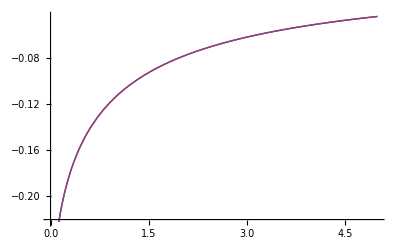

-0.0444483

2.3

```mathematica
Flong[x_,y_]:=1/((1-x)(1-y)) + x^2Log[x]/((1-x)^2(x-y)) + y^2Log[y]/((1-y)^2(y-x))
Glong[x_,y_]:=1/((1-x)(1-y)) + x Log[x]/((1-x)^2(x-y)) + y Log[y]/((1-y)^2(y-x))
Gcalc[x_]:=(1-x+x Log[x])/(x-1)^2
Gtwo[x_,y_]:=(Gcalc[x]-Gcalc[y])/(x-y)
Plot[{Glong[x,2],Gtwo[x,2]},{x,0,5}]
Expand[Flong[x,y]];
Glong[2.,5]
gl2f
```